```mathematica
connectOneBarabasiAlbert[g_Graph/;ConnectedGraphQ[g]]:=g;
connectOneBarabasiAlbert[g_Graph]:=Module[{cmps=ConnectedComponents[g],pos},
pos=Flatten[Intersection[Position[VertexInDegree[seed],0],Select[cmps,Length[#]==Min[Length/@cmps]&]]];
If[pos=={},g,
EdgeAdd[g,RandomChoice[{1,2,3}]->RandomChoice[pos]]
]
]
```

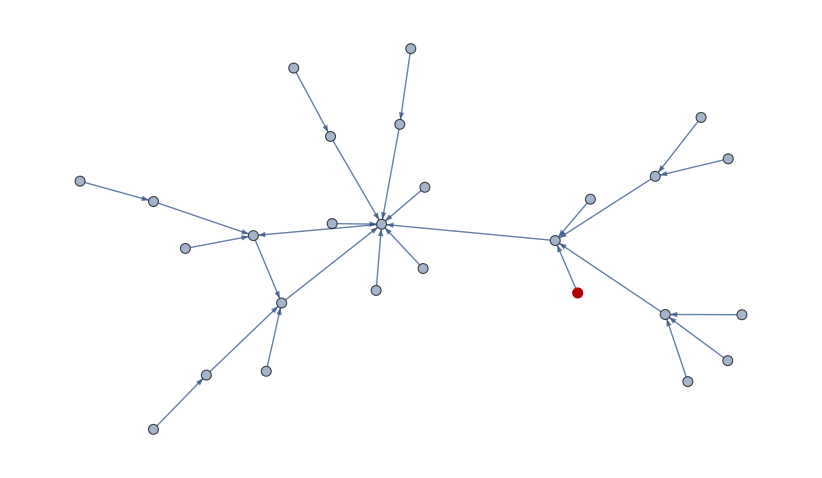

```mathematica
HighlightGraph[seed,27]
```

```mathematica
ConnectedComponents[seed]
```

{{1,2,3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27}}

```mathematica
Position[VertexInDegree[seed],0]
```

{{5},{10},{12},{13},{14},{15},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27}}

```mathematica
Length/@ConnectedComponents[seed]
```

{3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Min[Length/@ConnectedComponents[seed]]
```

1

```mathematica
Select[ConnectedComponents[seed],Length[#]==Min[Length/@ConnectedComponents[seed]]&]
```

{{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27}}

```mathematica
Intersection[Position[VertexInDegree[seed],0],Select[ConnectedComponents[seed],Length[#]==Min[Length/@ConnectedComponents[seed]]&]]
```

{{5},{10},{12},{13},{14},{15},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27}}

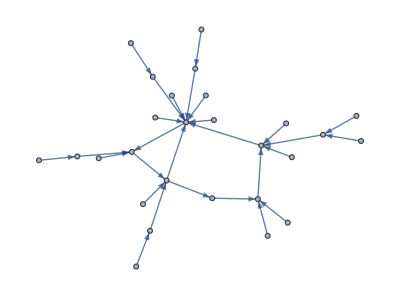

```mathematica
EdgeAdd[seed,RandomChoice[{1,2,3}]->RandomChoice[Flatten[Intersection[Position[VertexInDegree[seed],0],Select[ConnectedComponents[seed],Length[#]==Min[Length/@ConnectedComponents[seed]]&]]]]]
```

```mathematica
ConnectedComponents[%]
```

{{1,2,3,6,9,10},{4},{5},{7},{8},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27}}

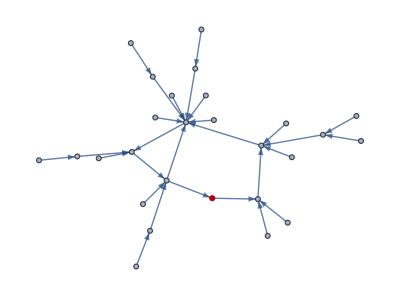

```mathematica
HighlightGraph[%%,10]
```

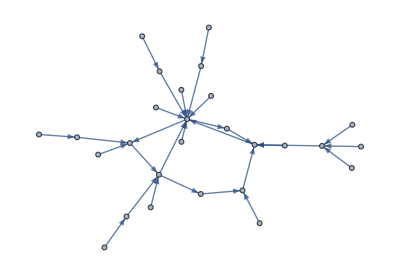

```mathematica
EdgeAdd[%%%,RandomChoice[{1,2,3}]->26]
```

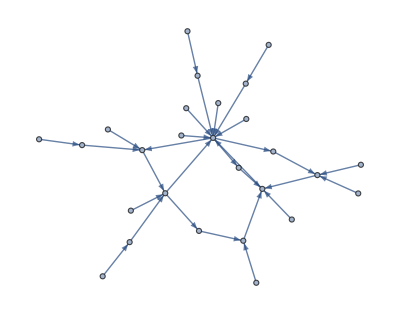

```mathematica
EdgeAdd[%,RandomChoice[{1,2,3}]->25]
```

```mathematica
ConnectedComponents[%]
```

{{1,2,3,6,9,16,25,26,27},{4},{5},{7},{8},{10},{11},{12},{13},{14},{15},{17},{18},{19},{20},{21},{22},{23},{24}}

```mathematica
tst={{0,1,1,1,1},{0,0,1,1,0},{0,1,0,1,1},{1,1,0,0,0},{0,0,0,1,0}};
```

```mathematica
tst=AdjacencyGraph[tst]
```

-Graphics-

```mathematica
Partition[Range[10],2]
```

{{1,2},{3,4},{5,6},{7,8},{9,10}}

```mathematica
graph=graphToNet[tst,Partition[Range[10],2]]
```

{{{1,2},{2,3,4,5}},{{3,4},{3,4,5}},{{5,6},{2,4}},{{7,8},{1,3}},{{9,10},{4}}}

```mathematica
M=Length[graph]
```

5

```mathematica
rem=remove[graph,Sort[RandomSample[Range[M],4]]]
```

{{1,3},{3,4},{4,3},{5,4}}

```mathematica
add[graph,rem]
```

{{{},{1}},{{},{}},{{1,7},{5}},{{5,9},{7}},{{},{9}}}

```mathematica
updateGraph[graph,%]
```

{{{2},{2,3,4,5}},{{3,4},{3,4,5}},{{6,1,7},{2,4}},{{8,5,9},{1,3}},{{10},{4}}}

```mathematica
updateGraph[graph,add[graph,remove[graph,Range[Length[graph]]]]]
```

{{{2,7},{2,3,4,5}},{{4,5},{3,4,5}},{{6,1},{2,4}},{{8,3,9},{1,3}},{{10},{4}}}

```mathematica
graph
```

{{{1,2},{2,3,4,5}},{{3,4},{3,4,5}},{{5,6},{2,4}},{{7,8},{1,3}},{{9,10},{4}}}

```mathematica
packs=graph[[All,1]]
```

{{1,2},{3,4},{5,6},{7,8},{9,10}}

```mathematica
Table[Drop[packs[[i]],Length[%39[[i,2]]]],{i,M}]
```

{{2},{4},{6},{7,8},{10}}

```mathematica
Table[Flatten[Append[%44[[i]],%39[[i,1]]]],{i,M}]
```

{{2},{4},{6,1},{7,8,5,9},{10,3}}

```mathematica
Transpose[{%46,graph[[All,2]]}]
```

{{{2},{2,3,4,5}},{{4},{3,4,5}},{{6,1},{2,4}},{{7,8,5,9},{1,3}},{{10,3},{4}}}

```mathematica
netEvolve[graph,1,5]
```

Part::partw: Part 2 of {{1,5}} does not exist.

Part::partw: Part 3 of {{1,5}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Drop::drop: Cannot drop positions 1 through 3 in {3,4}.

Drop::drop: Cannot drop positions 1 through 3 in {5,6}.

Drop::drop: Cannot drop positions 1 through 3 in {7,8}.

General::stop: Further output of Drop::drop will be suppressed during this calculation.

Part::pkspec1: The expression i cannot be used as a part specification.

RandomChoice::lrwl: The items for choice {{{2},{2,3,4,5}},{Drop[{3,4},3,{}],{3,4,5}},{Drop[{5,6},3,{}],{2,4}},{Drop[{7,8},3,{}],{1,3}},{Drop[{9,10},3,{1}],{4}}}⟦i,2⟧ should be a non-empty list or a rule weights -> choices.

Drop::argm: Drop called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Drop::argm will be suppressed during this calculation.

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 3 in Drop[{2},3,{2,{3,4},2,2,{7,8},{3,4},2,2,{3,4},2,«5»}].

Drop::normal: Nonatomic expression expected at position 1 in Drop[3,{2,{3,4},2,2,{7,8},{3,4},2,2,{3,4},2,«5»}].

Drop::normal: Nonatomic expression expected at position 1 in Drop[3,{2,{3,4},2,2,{7,8},{3,4},2,2,{3,4},2,«5»},{}].

Part::pkspec1: The expression i cannot be used as a part specification.

RandomChoice::lrwl: The items for choice {{Drop[3,{2,{3,4},2,2,{7,8},{3,4},2,2,{3,4},2,«5»},{}],{2,3,4,5}},{{2,2,2,2,2,2,3,4,2,2,«20»},{3,4,5}},{{2,2,2,3,4,3,4,2,3,4,«68»},{2,4}},{{2,2,2,3,4,5,6,2,3,4,«41»},{1,3}},{{2,2,2,3,4,7,8,2,3,4,«18»},{4}}}⟦i,2⟧ should be a non-empty list or a rule weights -> choices.

{{{{1,2},{2,3,4,5}},{{3,4},{3,4,5}},{{5,6},{2,4}},{{7,8},{1,3}},{{9,10},{4}}},{{{2},{2,3,4,5}},{Drop[{3,4},3,{}],{3,4,5}},{Drop[{5,6},3,{}],{2,4}},{Drop[{7,8},3,{}],{1,3}},{Drop[{9,10},3,{1}],{4}}},{{Drop[{2},3,{2,{3,4},2,2,{7,8},{3,4},2,2,{3,4},2,2,{9,10},2,{5,6},2}],{2,3,4,5}},3,1},{1},{1},{{{2,3,3,2,2,3},{2,3,4,5}},4}}
 |  |  |  |

```mathematica
%[[1]]
```

{{{1,2},{2,3,4,5}},{{3,4},{3,4,5}},{{5,6},{2,4}},{{7,8},{1,3}},{{9,10},{4}}}

```mathematica
%45[[2]]
```

{{{2},{2,3,4,5}},{{4,1,5},{3,4,5}},{{6,7},{2,4}},{{8,3,9},{1,3}},{{10},{4}}}

```mathematica
%45[[3]]
```

{{{},{2,3,4,5}},{{1,5},{3,4,5}},{{7,8},{2,4}},{{3,9,4,6,10},{1,3}},{{2},{4}}}

```mathematica
%45[[4]]
```

{{{},{2,3,4,5}},{{5},{3,4,5}},{{8,3},{2,4}},{{9,4,6,10,1,7,2},{1,3}},{{},{4}}}

```mathematica
%45[[5]]
```

{{{},{2,3,4,5}},{{},{3,4,5}},{{3,9},{2,4}},{{4,6,10,1,7,2,5,8},{1,3}},{{},{4}}}

```mathematica
Δ
```

{{{},{2,3}},{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{1}},{{},{2}}}

```mathematica
updateGraph[#,add[#,remove[#,Sort[RandomSample[Range[M],P]]]]]
```

```mathematica
Sort[RandomSample[Range[M],1]]
```

{1}

```mathematica
remove[Δ,%]
```

{{1,2}}

```mathematica
add[Δ,%53]
```

This is out {{1,2}}

This is r {{1},{},{}}

This is δ {{},{1},{}}

{{{},{1}},{{1},{}},{{},{}}}

```mathematica
updateGraph[Δ,%78]
```

{{{2,3,4},{2,3}},{{1},{1}},{{},{2}}}

```mathematica
%==Δ
```

True

```mathematica
netEvolve[Δ,1,3]
```

{{{{1,2,3,4},{2,3}},{{},{1}},{{},{2}}},{{{2,3,4},{2,3}},{{1},{1}},{{},{2}}},{{{2,3,4},{2,3}},{{1},{1}},{{},{2}}},{{{3,4},{2,3}},{{1},{1}},{{2},{2}}}}